# Accuracy of series approximations to the error function

## Katharine Long Texas Tech University

Here we compare two series approximations to the error function

The Maclaurin series erf(x)=2/(√π)(Σ_(n=0)^∞(-1))^n x^(2n+1)/(n!(2n+1)) which is convergent for all x but useful for |x|≲2.

The asymptotic series erf(x)∼ 1 - (e^(-x^2))/(√π x)[1+((Σ^∞)_(n=1)(-1))^n((2n-1)!!)/(2^n x^(2n))] which is divergent for all x but is useful for |x|≳3-4.

Note: For high-accuracy calculations, neither of these methods should be used as-is. An acceleration method such as the Shanks transformation (https://en.wikipedia.org/wiki/Shanks_transformation) should be used. Alternatively, a error-minimizing method such as a Chebyshev polynomial expansion can be used.

## Error in Maclaurin expansion for erf(x)

This series converges for all x, so in principle can produce accurate results for any x. However, for large x it can take very many terms to reach a small error, making it unsatisfactory as a practical method for |x| larger than about 2.

The Maclaurin series for erf(x) is a convergent alternating series, so the error after N terms is bounded by the N+1-th term.

```mathematica
Subscript[e, n_][x_]=2/Sqrt[Pi] x^(2n+1)/n!/(2n+1)
```

(2 x^(2 n+1))/(√π (2 n+1) n!)

```mathematica
eHalf=Table[{n,Subscript[e, n][1/2]},{n,0,100}];
```

```mathematica
e1=Table[{n,Subscript[e, n][1]},{n,0,100}];
```

```mathematica
e2=Table[{n,Subscript[e, n][2]},{n,0,100}];
```

```mathematica
e4=Table[{n,Subscript[e, n][4]},{n,0,100}];
```

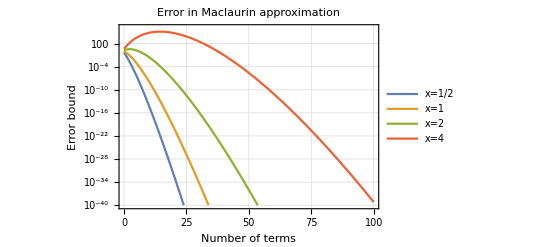

```mathematica
ListLogPlot[{eHalf,e1,e2,e4},GridLines->Automatic,Joined->True,PlotLegends->{"x=1/2","x=1","x=2","x=4"},
FrameLabel->{"Number of terms","Error bound"},
PlotLabel->"Error in Maclaurin approximation",PlotRange->{10^-40,10^6}]
```

## Error in asymptotic expansion for erf(x)

This series diverges for all x, but a partial sum can still provide an accurate approximation for |x| larger than about 4.

```mathematica
Subscript[ae, n_][x_]=1/Sqrt[Pi]/x^(2n+1)(2n-1)!!/2^n Exp[-x^2]
```

(2^-n ⅇ^(-x^2) (2 n-1)!! x^(-2 n-1))/(√π)

```mathematica
ae2 = Table[{n,Subscript[ae, n][2]},{n,1,60}];
```

```mathematica
ae4 = Table[{n,Subscript[ae, n][4]},{n,1,60}];
```

```mathematica
ae6 = Table[{n,Subscript[ae, n][6]},{n,1,60}];
```

```mathematica
ae8 = Table[{n,Subscript[ae, n][8]},{n,1,60}];
```

```mathematica
ListLogPlot[{ae2,ae4,ae6},PlotRange->{10^-40,1},Joined->True,PlotMarkers->{Automatic,Tiny},FrameLabel->{"Number of terms","Error bound"},
PlotLabel->"Error in asymptotic approximation",
PlotLegends->{"x=2","x=4","x=6"},GridLines->Automatic]
```

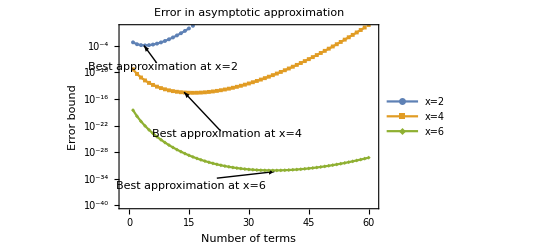

The asymptotic series for erf(x) does not converge as n→ ∞. However, a truncated series can still provide a good approximation to erf(x). For a chosen value of x, add terms to the approximation as long as the terms decrease in magnitude.

Note: The phrase “best approximation” in the labels above means that this the smallest error that can be obtained using the asymptotic series without modification. A method such as an iterated Shanks transformation can be used to obtain smaller errors.